```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
(*FAILURE*)
```

# Free energy For SRO that matches Experimental predictions

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*The sequence of things that I am going to do
1. Rotation of a 1D function (DONE)
2. Rotation of a 2D function (DONE)
3. Create a free energy that has 2 wells and 1 touching point
4. Add temperature dependence to reproduce the desired stress vs Transition temperature behaviour
5. Find a way to generate an asymmetric function with compact support. Likely take a symmetric function and then unevenly squeeze the axes.
a. Create a 1D skew function, subtract it from a quadratic well and see if it creates a touching point.
-Graphics-
*)
```

## (*Rotation of a 1D function*)

```mathematica
(*Given the graph of a function
(x,f(x))
We want the graph
(x,g(x))
were g(x) can be thought of a f(x) rotated version of f(x).
-Graphics-
The way to achieve this is to rotate the axes, to get the primed axes which are related to the original axes by the relation
   [x'] = [cosθ -sinθ][x]
[y']   [sinθ  cosθ][y]
   
where the above has to be thought interms of a matrix equation.
If we apply this to the graph (x,f(x)) we get the graph
(x',f'(x'))=(xcosθ-f(x)sinθ,xsinθ+f(x)cosθ)
The graph is parametrized by x, the variable describing the original axes.
We could try to get an explicit dependence, which could be obtained by solving the equation
x'=xcosθ-f(x)sinθ
Let us represent the solution as x=u(x')
We can plug this into the second equation to get
f'(x')=u(x')sinθ+f(u(x'))cosθ
*)
```

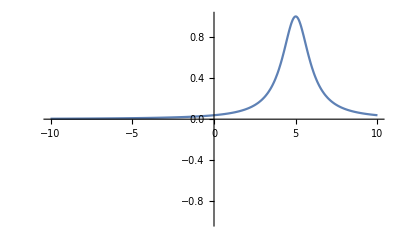

{{x→Root[-√2-52 x1+(26 √2+20 x1) #1+(-10 √2-2 x1) #1^2+√2 #1^3&,1]}}

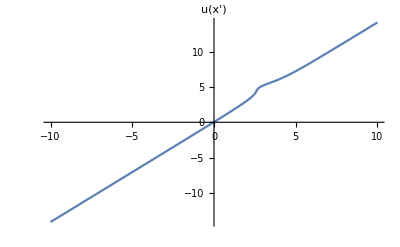

-Graphics-

```mathematica
f1[x_,A_]:=A/(1+(x-5)^2)
θ1:=π/4
AA:=1
Plot[f1[x,AA],{x,-10,10},PlotRange->{-AA,AA}]
Soln1=Solve[x1==x*Cos[θ1]-f1[x,AA]*Sin[θ1],x,Reals] (*Here x' is set as x1*)
u[x1_]:=x/.Soln1
Plot[u[x1],{x1,-10,10},AxesLabel->"u(x')"](*Plotting u[x']*)
g[x1_]:=u[x1]*Sin[θ1]+f1[u[x1]]*Cos[θ1]
Plot[g[x1],{x1,-10,10},AxesLabel->"f'(x')"](*Plotting f'[x']*)
```

### (*Minimization problem*)

```mathematica
bartab1=Table[{i},{i,0,60,1}];
Plot[(1+x1^2)-g[x1],{x1,-10,10}]
(*Manipulate[Soln1=NMinimize[(1+x1^2)-g[x1]-s*x1,x1,Method->{"Automatic","InitialPoints"->bartab1}];Plot[{s*(x1)+Soln1[[1]],(1+x1^2)-g[x1]},{x1,-20,100},PlotRange->{-10,30}],{a,0,100},{b,0,1/12},{s,0,1,0.01}](*The bartab which contains all initial points is really successful method for doing this osrt of minimization*)*)
```

-Graphics-

## (*Rotation of a 2D function*)

```mathematica
(*Given the graph of a function
(x,y,f(x,y))
We want the graph
(x,y,g(x,y))
were g(x,y) can be thought of as a rotated version of f(x,y).
The way to achieve this is to rotate the axes, to get the primed axes which are related to the original axes by the relation
[x']   [ cosθ 0 -sinθ][x]
   [y'] = [  0   1    0 ][y]
[z']   [-sinθ 0  cosθ][z]
where the above has to be thought interms of a matrix equation.
If we apply this to the graph (x,f(x)) we get the graph
(x',y',f'(x'))=(xcosθ-f(x,y)sinθ,y,xsinθ+f(x,y)cosθ)
The graph is parametrized by x&y, the variable describing the original axes.
We could try to get an explicit dependence, which could be obtained by solving the equation
x'=xcosθ-f(x,y)sinθ=xcosθ-f(x,y')sinθ
where we used the fact that y=y'.
Let us represent the solution as x=u(x',y')
We can plug this into the second equation to get
f'(x',y')=u(x',y')sinθ+f(u(x',y'),y')cosθ
*)
```

```mathematica
f2[x_,y_]:=1/(1+y^2+x^2)
θ2:=π/4
Plot3D[f2[x,y],{x,-10,10},{y,-10,10},PlotRange->{-1,1}]
Soln2=Solve[x2==x*Cos[θ2]-f2[x,y2]*Sin[θ2],x,Reals] (*Here x' is set as x2 and y' is set as y2*)
u2[x2_,y2_]:=x/.Soln2
Plot3D[u2[x2,y2],{x2,-10,10},{y2,-10,10},AxesLabel->"u(x',y')"](*Plotting u[x',y']*)
g2[x2_,y2_]:=u2[x2,y2]*Sin[θ2]+f2[u2[x2,y2],y2]*Cos[θ2]
Plot3D[g2[x2,y2],{x2,-10,10},{y2,-10,10},AxesLabel->"f'(x',y')"](*Plotting f'[x']*)
```

-Graphics3D-

{{x→Root[-√2-2 x2-2 x2 y2^2+(√2+√2 y2^2) #1-2 x2 #1^2+√2 #1^3&,1]}}

-Graphics3D-

-Graphics3D-

## (*Create a 3D function with 2 wells and 1 Touching point*)

```mathematica
(*We want to create a free energy that has 3 touching points when stressed. The way to do this is to position the wells appropriately.
In order to achieve this, we will follow the following steps:-
a. Create a 1D function that has two wells, such that (DONE)
     I. The lowest well is at x=0 with energy=0 
    II. There is a systematic way of controlling the energy of the 2nd well wrt the energy of the first; my thought is to introduce a linear term
   b. Convexify the probelm to get a 2D function. (DONE)
   c. Create a touching point by subtracting the tilted function in the above example.1
*)
```

```mathematica
(*3a. 1D fn with desired manipulatable wells*)
f3[x_,a_,b_]:=x^4-a*x^3+a^2(1/4+b)*x^2+1
Manipulate[Plot[f3[x,a,b],{x,-2,10}],{a,0,50},{b,0,1/32}]
(*To get a function ϕ[x] which is 0 at x=0 and has a root at x=0, we set
f[x]=x^4-ax^3+bx^2+cx+d
f[0]=0=>d=0 this ensures the function is 0 at x=0
f'[0]=0=>c=0, this ensures that one of the roots is at x=0
The roots of f'[x]=0 are the sol;utions to the equation
x(4 x^2-3ax+2b)=0
We now need ot ensure that both roots of the quadratic are positive
x=(3a+/-\sqrt[9 a^2-32b])/8
Note that the roots are real valued if 
9 a^2-32b>0
This ensured that they are positive valued  if b>0, as
3a>\sqrt[9 a^2-32b]
Now the second well can be lower or higher than the first well
As of now we have
f[x]=x^4-ax^3+bx^2+1
The second well is at height 1, so for it to be higher, we need
f[x]>=1 \forall x
This boils down to 
x^4-ax^3+bx^2>=0=>x^2(x^2-ax+b)>=0
The first term is always positive, thus we need the second term to be positive, this give us
(x^2-ax+b)>=0 =>(x-a/2)^2+(b-a^2/4)>=0
Thus the function is positive if we have (b-a^2/4)>=0
The constraints on b is
1/4*a^2<b<9/32 a^2
If we set b=1/4*a^2+a^2\tilde{b}, we can write the constraint on \tilde{b} as
0<\tilde{b}<1/32
The final form of the free energy with \tilde{b}\mapsto b can be written as
f[x]=x^4-ax^3+a^2(1/4+b)x^2+1
*)
Manipulate[Plot[f3[x,a,b],{x,-2,10},PlotRange->{-10,10}],{b,0,1/32},{a,0.1,10}]
```

```mathematica
(*3b. Convexifying the 1D function, Introducing a touchoing point and testing the minimization*)
```

```mathematica
ϕ1[x_,y_,a_,b_]:=(f3[x,a,b])*(1+y^2)
Manipulate[Plot3D[ϕ1[x,y,a,b],{x,-10,30},{y,-5,5},PlotRange->{-5000,10000}],{b,0,1/32},{a,1,10}](*Plot of the 3D function*)
Manipulate[Plot[ϕ1[x,0,a,b],{x,-10,30},PlotRange->{-500,10000}],{b,0,1/32},{a,1,30}](*Plot of the slice y=0*)
(*Creating a touching point*)
Manipulate[Plot3D[10*Exp[-((x-5)/c)^2-((y-5)/d)^2],{x,3,7},{y,3,7},PlotRange->{-10,10}],{c,0.5,10},{d,0.5,10}]
g3[x_,y_,A_,c_,d_,r_]:=Piecewise[{{A*Exp[1/((x-c)^2+(y-d)^2-r^2)]*Exp[1/r^2],(x-c)^2+(y-d)^2-r^2<0},{0,(x-c)^2+(y-d)^2-r^2>0}}]
Manipulate[Plot3D[g3[x,y,A,3,3,r],{x,0,7},{y,0,7}],{r,0.5,1},{A,0,10}]
ϕ2[x_,y_,a_,b_,A_]:=(f3[x,a,b])*(1+y^2)-g3[x,y,A,5,5,0.5]
ϕ3[x_,y_,a_,b_,A_,c_,d_,r_]:=(f3[x,a,b])*(1+y^2)-g3[x,y,A,c,d,r]
Manipulate[Plot3D[ϕ2[x,y,a,b,A],{x,-10,30},{y,-7,7},PlotRange->{-5000,1000000}],{b,0,1/32},{a,1,50},{A,1,100000000}]
```

```mathematica
(*We now solve the minimization problem
inf \varphi(x,y)-σx*)
```

```mathematica
x13=0;xN3=20;Δx3=1;
y13=0;yN3=20;Δy3=1;
bartab3=Join@@Table[{i,j},{i,x13,xN3,Δx3},{j,y13,yN3,Δy3}];
Manipulate[Soln3=NMinimize[{ϕ3[x,y,a,b,A,c,d,r]-s*x,y>=0},{x,y},Method->{"Automatic","InitialPoints"->bartab3}];{Plot3D[{s*(x)+Soln3[[1]],ϕ3[x,y,a,b,A,c,d,r]},{x,-20,20},{y,-5,5},PlotRange->{-50000,100000}],Soln3[[2]]},{a,27},{b,0.02434842249},{A,1,50000},{c,3},{d,3},{r,0.5},{s,0,1000}](*With A=0, there is a tructural phase transition*)
```

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab3, changed to Automatic.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,27,0.0243484,1,3,3,0.5] is not a number at {x,y} = {0.918621,1.66351}.

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab3, changed to Automatic.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,27,0.0243484,1,3,3,0.5] is not a number at {x,y} = {0.918621,1.66351}.

NMinimize::ivar: -19.9971 is not a valid variable.

NMinimize::ivar: -17.14 is not a valid variable.

NMinimize::ivar: -14.2829 is not a valid variable.

General::stop: Further output of NMinimize::ivar will be suppressed during this calculation.

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab3, changed to Automatic.

General::stop: Further output of NMinimize::parchange will be suppressed during this calculation.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,27,0.0243484,1,3,3,0.5] is not a number at {x,y} = {0.918621,1.66351}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

```mathematica
(*Introducing Temperature dependence*)
```

```mathematica
(*Here I want to introduce a temperature dependence which captures the stress vs transition temperature of the wells. There are two aspects to this behaviour.
1. There is an initial Quadratic behaviour for the stress vs transition temperature
2. Then there is a linear decrease. 
The two wells and touching point (here represented as a well) will be labelled as N1,S and N2 respectively.
The way i am going to do this is to get the functional dependence of s on (c,d).
Since we expect a quadratic behaviour, we know that Subscript[θ, c](σ)=kσ^2+Subscript[θ, c](0)
From these two, we cna get (c(θ),d(θ)).*)
a1=27;
b1=0.02434842249;
A1=11527;(*11528 is the value at which the S is just above the Normal well.*)
r1=0.5;
x14=0;xN4=20;Δx4=1;
y14=0;yN4=20;Δy4=1;
bartab4=Join@@Table[{i,j},{i,x14,xN4,Δx4},{j,y14,yN4,Δy4}];
Manipulate[Soln4=NMinimize[{ϕ3[x,y,a1,b1,A1,3-c1,3-d1,r1]-s*x,y>=0},{x,y},Method->{"Automatic","InitialPoints"->bartab4}];{Plot3D[{s*(x)+Soln4[[1]],ϕ3[x,y,a1,b1,A1,3-c1,3-d1,r1]},{x,-20,20},{y,-5,5},PlotRange->{-50000,100000}],Soln4[[2]]},{c1,0,1},{d1,0,1},{s,0,1000}]
```

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab4, changed to Automatic.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,a1,b1,A1,3,3,r1] is not a number at {x,y} = {0.918621,1.66351}.

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab4, changed to Automatic.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,a1,b1,A1,3,3,r1] is not a number at {x,y} = {0.918621,1.66351}.

NMinimize::ivar: -19.9971 is not a valid variable.

NMinimize::ivar: -17.14 is not a valid variable.

NMinimize::ivar: -14.2829 is not a valid variable.

General::stop: Further output of NMinimize::ivar will be suppressed during this calculation.

NMinimize::parchange: Inappropriate parameter: InitialPoints -> bartab4, changed to Automatic.

General::stop: Further output of NMinimize::parchange will be suppressed during this calculation.

NMinimize::nnum: The function value ϕ3[0.918621,1.66351,a1,b1,A1,3,3,r1] is not a number at {x,y} = {0.918621,1.66351}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

```mathematica
(*5. Create a 3D function with 2 wells and 1 Touching point*)
```

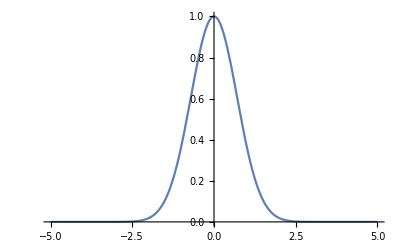

```mathematica
f5[x_]:=Exp[-x^2]
Plot[f5[x],{x,-5,5}]
T[x_,a_,b_]:=Piecewise[{{a*x^2,x>0},{b*x^2,x<=0}}]
Manipulate[Plot[f5[T[x-c,a,b]],{x,-10,10},PlotRange->{-2,2}],{a,0.1,2},{b,0.1,2},{c,2,3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[Root[-3.99197×10^23-6.67195×10^24 x1+(4.71778×10^24+2.56614×10^24 x1) #1+(-1.81453×10^24-2.56614×10^23 x1) #1^2+1.81453×10^23 #1^3&,1], 1.89455<x1<2.05384||x1>2.05384||x1<1.89455]},{x→ConditionalExpression[Root[-3.99197×10^23-6.67195×10^24 x1+(4.71778×10^24+2.56614×10^24 x1) #1+(-1.81453×10^24-2.56614×10^23 x1) #1^2+1.81453×10^23 #1^3&,2], 1.89455<x1<2.05384]},{x→ConditionalExpression[Root[-3.99197×10^23-6.67195×10^24 x1+(4.71778×10^24+2.56614×10^24 x1) #1+(-1.81453×10^24-2.56614×10^23 x1) #1^2+1.81453×10^23 #1^3&,3], 1.89455<x1<2.05384]}}

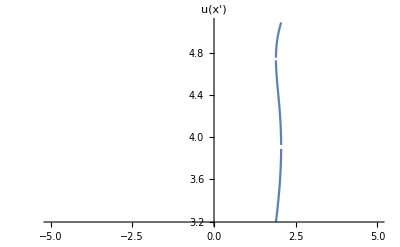

```mathematica
Solution=Solve[x1==x*Cos[θ1]-f1[x,2.2]*Sin[θ1],x,Reals]
u5[x1_]:=x/.Solution
Plot[u5[x1],{x1,-5,5},AxesLabel->"u(x')"](*Plotting u[x']*)
```